# Sympathetic Cooling Last Updated: 3/15/2021

```mathematica
Remove["Global`*"];
```

## 1 Get eigen

## 1.1 Setup

```mathematica
m=Append[ConstantArray[m0,13],m1];(*m=ConstantArray[m0,13];*)
wmhz=2*Pi*1*^6;ke2=2.306569*^-28;Num =Length[m];l0=(ke2/kz)^(1/3);
kM =Append[ Array[k,{2,2}],{kz,kz}];kM=Transpose[If[#===m0,kM[[1;;,1]],kM[[1;;,2]]]&/@m];
xM = Array[x,{3,Num}];z0M = Array[z0,Num];
L0EQ [i_]:=z0M[[i]]==(Sum[(z0M[[i]] - z0M[[k]])^(-2),{k,1,i-1}] - Sum[(z0M[[i]] - z0M[[k]])^(-2),{k, i+1,Num}])
L0EQlist =L0EQ/@Range[Num];magic=Range[-3.5,3.5,7/(Num-1)];pos=Table[{z0M[[i]],magic[[i]]},{i,Num}];
z0M=z0M/.Chop[FindRoot[L0EQlist,pos]];

L0Mn[i_,j_,n_]:=If[i==j,0,Abs[z0M[[i]]-z0M[[j]]]^n]
ics=ArrayReshape[Append[Table[xM[[d,i]]->0,{d,2},{i,Num}],Table[(xM[[3,i]]-xM[[3,j]])->L0Mn[i,j,1]*l0,{i,Num},{j,i+1,Num}]],{Num*(Num+3)/2}];
Uel=0.5*Total[kM*(xM^2),2]+ke2*Sum[(Total[(xM[[;;,i]]-xM[[;;,j]])^2])^(-0.5),{i,Num},{j,i+1,Num}];
Vel1=-Table[D[Uel,{xM[[d,i]]},{xM[[d,j]]}]/Sqrt[m[[i]]*m[[j]]],{d,3},{i,Num},{j,Num}]/.ics//FullSimplify;
Vel1norm=Vel1/.{m1->m0,k[1,2]->k[1,1],k[2,2]->k[2,1]}//FullSimplify;
{k[1,1],k[1,2]}=κr^2*3.25*^-40*V0^2/w^2/r0^4/{m0,m1}+1.602*^-13*(κr*V1/r0^2-κz*U/z0^2)//FullSimplify;
{k[2,1],k[2,2]}=κr^2*3.25*^-40*V0^2/w^2/r0^4/{m0,m1}+1.602*^-13*(-κr*V1/r0^2-κz*U/z0^2)//FullSimplify;
kz=3.204*^-13*κz*U/z0^2//FullSimplify;
k1Clean={k[1,1],k[1,2]}/.{m1->m1tmp};Vel1clean=Vel1[[1]]/.{m1->m1tmp};
```

```mathematica
(**)
Clear[V0,V1,U,w,m1,m1hold,r0,z0,vlistnorm,vvals,wmvals,eigenholder];
m0=138*1.66054*^-27;m1hold=139*1.66054*^-27;κr=1;κz=1;r0=6.81;z0=10.2;(**)
(**)
solnsMOTION={V0->5,V1->0,U->0.3,w->0.016};
eigenholder=Table[Eigensystem[Vel1[[d]]/.solnsMOTION/.{m1->m1hold}],{d,3}];
wmvals=Sqrt[-eigenholder[[;;,1]]]/wmhz//FullSimplify;vvals=eigenholder[[;;,2]]//FullSimplify;
eigenholder=Table[Eigensystem[Vel1[[d]]/.solnsMOTION/.{m1->m0}],{d,3}];
wmlistnorm=Sqrt[-eigenholder[[;;,1]]]/wmhz//FullSimplify;vlistnorm=Chop[eigenholder[[;;,2]]/.{V0->1,V1->0,U->1,w->1}//FullSimplify];vlistnorm=Table[Normalize[vlistnorm[[d,i]]],{d,3},{i,Num}]//FullSimplify;
m1=m1hold;

solnsDJ=solnsMOTION;
wsecvals=Sqrt[{{k[1,1],k[1,2]/a},{k[2,1],k[2,2]/a},kz/{m0,m1}}]/wmhz/.solnsDJ;
qx=8.11582681*^-27*V0/w^2/r0^2/{m0,m1}/.solnsDJ;
gim=Table[Transpose[vvals[[d]]],{d,3}];
```

## 2 Quantum Approach

## 2.1 Quantum (low temp)

```mathematica
(*prep*)
Vel1vals=-Vel1/.solnsMOTION;ree=8*20*wmhz/(5*(wmhz*20)^2);raa=1.07613*^-12;(*1.2744*^7*)
getNAvg[temp_]:=1/(Exp[4.8*^-5/temp*Flatten[wmvals[[1]]]]-1);
tempK=1*^-1;thermstate=Round[getNAvg[tempK]];
```

```mathematica
(*cool*)
sympcool[nm_,i_,j_]:=Sum[gim[[1,j,md]]^2*gim[[1,i,md]]^2*((nm[[md]]+0.5)*ree-7/10/wmvals[[1,md]]/wmhz)*(wmhz^2*wmvals[[1,md]]^2+Sum[Vel1vals[[1,j,jd]]*gim[[1,jd,md]]/gim[[1,j,md]],{jd,Num}]),{md,Num}]/Sum[gim[[1,i,md]]^4*((nm[[md]]+0.5)*ree-7/10/wmvals[[1,md]]/wmhz)*(wmvals[[1,md]]^2*wmhz^2+Sum[Vel1vals[[1,i,jd]]*gim[[1,jd,md]]/gim[[1,i,md]],{jd,Num}]),{md,Num}]

(*cooling all ions*)
nmdot[nm_]:=Sum[gim[[1,i]]^2/m[[i]]*((nm+0.5)*ree-7/10/wmvals[[1]]/wmhz),{i,Num-1}];
sympcoolIND[nm_,i_]:=Sum[gim[[1,i,md]]^2*nmdot[nm][[md]]*(wmvals[[1,md]]^2*wmhz^2+Sum[Vel1vals[[1,i,jd]]*gim[[1,jd,md]]/gim[[1,i,md]],{jd,Num}]),{md,Num}]
rescool=(sympcoolIND[thermstate,#]&/@Range[Num]*100)/sympcoolIND[thermstate,7];
```

```mathematica
(*plot - all cool, different mass ratios*)
AllSympCoolDiffMass[mass_]:=Module[{Vel1valstmp=-Vel1clean/.solnsMOTION/.{m1tmp->mass}},
{wmtmp,vtmp}=Eigensystem[Vel1clean/.solnsMOTION/.{m1tmp->mass}];wmtmp=Sqrt[-wmtmp]/wmhz;gimtmp=Transpose[vtmp];
nmdottmp[nm_]:=Sum[gimtmp[[i]]^2/m[[i]]*((nm+0.5)*ree-7/10/wmtmp/wmhz),{i,Num-1}];
sympcoolINDtmp[nm_,i_]:=Sum[gimtmp[[i,md]]^2*nmdottmp[nm][[md]]*(wmtmp[[md]]^2*wmhz^2+Sum[Vel1valstmp[[i,jd]]*gimtmp[[jd,md]]/gimtmp[[i,md]],{jd,Num}]),{md,Num}];
getNAvgtmp[temp_]:=1/(Exp[4.8*^-5/temp*Flatten[wmtmp]]-1);stateDJ=getNAvgtmp[tempK/10];
(sympcoolINDtmp[stateDJ,#]&/@Range[Num]*100)/sympcoolINDtmp[stateDJ,Round[Num/2]]]
```

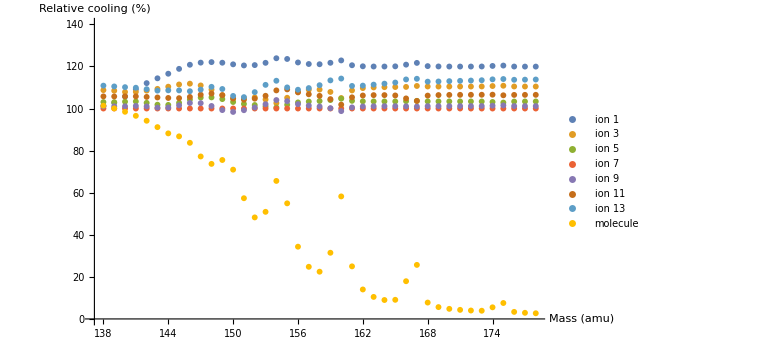
Sympathetic Cooling (all ions Doppler-cooled) as a percentage of ion 7 cooling rate @0.1K -Graphics-Top

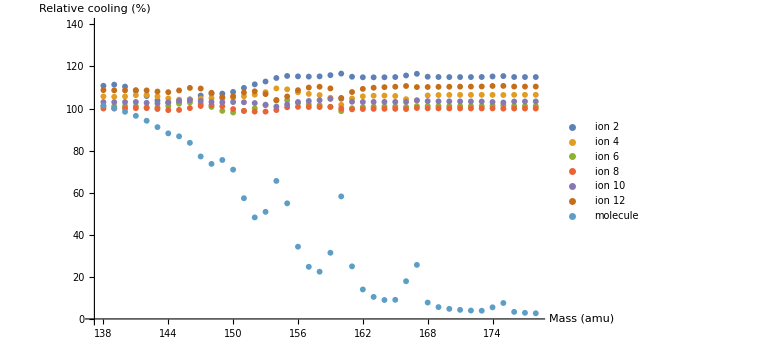
Sympathetic Cooling (all ions Doppler-cooled) as a percentage of ion 7 cooling rate @0.1K -Graphics-Top

```mathematica
startmass=138;endmass=178;
res1=Transpose[Parallelize[AllSympCoolDiffMass[#]&/@(1.66*^-27*Range[startmass,endmass])]];
Labeled[ListPlot[Append[res1[[#;;Num-1;;2]],res1[[Num]]],DataRange->{startmass,endmass},ImageSize->Large,PlotLegends->Append[Table["ion "<>ToString[i],{i,#,Num-1,2}],"molecule"],PlotRange->{0,140},Axes->True,AxesLabel->{"Mass (amu)","Relative cooling (%)"}]"Sympathetic Cooling (all ions Doppler-cooled) as a percentage of ion 7 cooling rate @"<>ToString[N[tempK]]<>"K",Top]&[1]
Labeled[ListPlot[Append[res1[[#;;Num-1;;2]],res1[[Num]]],DataRange->{startmass,endmass},ImageSize->Large,PlotLegends->Append[Table["ion "<>ToString[i],{i,#,Num-1,2}],"molecule"],PlotRange->{0,140},Axes->True,AxesLabel->{"Mass (amu)","Relative cooling (%)"}]"Sympathetic Cooling (all ions Doppler-cooled) as a percentage of ion 7 cooling rate @"<>ToString[N[tempK]]<>"K",Top]&[2]
```

## 2.2 Same for different configurations/length/mass

```mathematica
AllSCDiffMNO[mass_,N_,molloc_]:=Module[{massconfig=Insert[ConstantArray[m0,N-1],m1,molloc],magic=Range[-3.5,3.5,7/(N-1)],kM,z0M,z0,L0EQ,L0EQlist,z0Msum,matrix,wmvals,vvals,gim},
kM=If[#===m0,k1Clean[[1]],k1Clean[[2]]]&/@massconfig;
z0M=Array[z0,N];L0EQ [i_]:=z0M[[i]]==(Sum[(z0M[[i]] - z0M[[k]])^(-2),{k,1,i-1}] - Sum[(z0M[[i]] - z0M[[k]])^(-2),{k, i+1,N}]);
L0EQlist =L0EQ/@Range[N];z0M=z0M/.Chop[FindRoot[L0EQlist,Table[{z0M[[i]],magic[[i]]},{i,N}]]];
z0Msum=Table[Sum[If[i≠j,Abs[z0M[[i]]-z0M[[j]]]^(-3),0],{i,N}],{j,N}];
matrix=-kz*Table[If[i≠j,Abs[z0M[[i]]-z0M[[j]]]^(-3)/Sqrt[massconfig[[i]]*massconfig[[j]]],0],{i,N},{j,N}]-DiagonalMatrix[(kM-kz*z0Msum)/massconfig]/.solnsMOTION/.{m1tmp->mass};
{wmvals,vvals}=Eigensystem[matrix];wmvals=Sqrt[-wmvals]/wmhz;gim=Transpose[vvals];
nmdottmp[nm_]:=Sum[gim[[i]]^2/massconfig[[i]]*((nm+0.5)*ree-7/10/wmvals/wmhz),{i,N-1}];
sympcoolINDtmp[nm_,i_]:=Sum[gim[[i,md]]^2*nmdottmp[nm][[md]]*(wmvals[[md]]^2*wmhz^2+Sum[matrix[[i,jd]]*gim[[jd,md]]/gim[[i,md]],{jd,N}]),{md,N}];
getNAvgtmp[temp_]:=1/(Exp[4.8*^-5/temp*Flatten[wmvals]]-1);stateDJ=getNAvgtmp[tempK/10];
(sympcoolINDtmp[stateDJ,#]&/@Range[N]*100)/sympcoolINDtmp[stateDJ,Round[N/2]];vvals
]
```

```mathematica
Chop[AllSCDiffMNO[m1hold,14,14]+vvals[[1]]]
```

{{-0.585029,-0.57966,-0.574676,-0.569671,-0.564438,-0.558804,-0.552577,-0.545503,-0.537208,-0.527076,-0.513968,-0.495404,-0.464179,-0.376484},{0.963223,0.733378,0.546683,0.381766,0.230511,0.0887713,-0.045892,-0.174992,-0.299408,-0.419388,-0.534199,-0.640729,-0.727197,-0.711167},{1.03594,0.387653,-0.0176044,-0.283271,-0.448893,-0.534263,-0.550386,-0.503433,-0.396414,-0.229947,-0.00265238,0.288077,0.64076,0.974217},{-0.904794,0.155415,0.544674,0.609977,0.4947,0.280432,0.023317,-0.231844,-0.444229,-0.571651,-0.564835,-0.3588,0.142692,1.0576},{0.700655,-0.632075,-0.673584,-0.325426,0.0830205,0.399755,0.552891,0.517309,0.303151,-0.044235,-0.433367,-0.696248,-0.50613,0.887332},{-0.483049,0.908146,0.34131,-0.302897,-0.599426,-0.520886,-0.185744,0.231336,0.543253,0.583853,0.252443,-0.395493,-0.899582,0.591308},{0.290842,-0.922867,0.256822,0.695724,0.394923,-0.165825,-0.558829,-0.55248,-0.150947,0.407488,0.693897,0.237943,-0.934444,0.335598},{0.152967,-0.739736,0.759036,0.463598,-0.333606,-0.65147,-0.310087,0.313333,0.651588,0.330191,-0.466872,-0.756596,0.745509,-0.168855},{0.0704748,-0.488159,0.9332,-0.197147,-0.717819,-0.154185,0.553949,0.553547,-0.154903,-0.717884,-0.196341,0.933357,-0.489803,0.0756893},{-0.0283145,0.26936,-0.798489,0.773799,0.303427,-0.632383,-0.445079,0.445161,0.632327,-0.303538,-0.773745,0.798594,-0.269726,0.0298996},{-0.00977854,0.123949,-0.521942,0.93309,-0.488683,-0.56693,0.5303,0.530291,-0.566938,-0.488671,0.933096,-0.52196,0.12402,-0.010212},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-0.000644057,0.0135941,-0.100546,0.378103,-0.813033,0.985557,-0.463031,-0.463031,0.985557,-0.813033,0.378104,-0.100546,0.013596,-0.000663479},{0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
AllSympCoolDiffMass[m1hold]
AllSCDiffMNO[m1hold,14,14]
```

{102.806,111.33,108.424,105.573,103.007,101.057,100.,99.9862,101.032,103.027,105.723,108.63,110.47,99.9972}

{{-0.292515,-0.28983,-0.287338,-0.284835,-0.282219,-0.279402,-0.276288,-0.272752,-0.268604,-0.263538,-0.256984,-0.247702,-0.232089,-0.188242},{0.481612,0.366689,0.273341,0.190883,0.115256,0.0443857,-0.022946,-0.0874962,-0.149704,-0.209694,-0.267099,-0.320364,-0.363598,-0.355584},{0.517971,0.193827,-0.00880222,-0.141635,-0.224446,-0.267131,-0.275193,-0.251716,-0.198207,-0.114974,-0.00132619,0.144038,0.32038,0.487108},{-0.452397,0.0777076,0.272337,0.304988,0.24735,0.140216,0.0116585,-0.115922,-0.222115,-0.285826,-0.282418,-0.1794,0.071346,0.528802},{0.350328,-0.316038,-0.336792,-0.162713,0.0415102,0.199877,0.276445,0.258654,0.151576,-0.0221175,-0.216684,-0.348124,-0.253065,0.443666},{-0.241525,0.454073,0.170655,-0.151448,-0.299713,-0.260443,-0.0928722,0.115668,0.271627,0.291927,0.126222,-0.197747,-0.449791,0.295654},{0.145421,-0.461433,0.128411,0.347862,0.197462,-0.0829123,-0.279414,-0.27624,-0.0754734,0.203744,0.346949,0.118971,-0.467222,0.167799},{0.0764836,-0.369868,0.379518,0.231799,-0.166803,-0.325735,-0.155044,0.156666,0.325794,0.165095,-0.233436,-0.378298,0.372754,-0.0844274},{0.0352374,-0.24408,0.4666,-0.0985737,-0.358909,-0.0770927,0.276974,0.276774,-0.0774514,-0.358942,-0.0981707,0.466678,-0.244902,0.0378446},{-0.0141573,0.13468,-0.399245,0.3869,0.151713,-0.316191,-0.22254,0.222581,0.316163,-0.151769,-0.386873,0.399297,-0.134863,0.0149498},{-0.00488927,0.0619743,-0.260971,0.466545,-0.244341,-0.283465,0.26515,0.265146,-0.283469,-0.244336,0.466548,-0.26098,0.0620102,-0.00510601},{0.00141128,-0.0232937,0.132277,-0.358444,0.472979,-0.162259,-0.321618,0.321619,0.162258,-0.472979,0.358445,-0.132278,0.0233001,-0.00146233},{-0.000322029,0.00679704,-0.0502732,0.189052,-0.406517,0.492778,-0.231515,-0.231515,0.492778,-0.406517,0.189052,-0.0502732,0.006798,-0.000331739},{0.0000504388,-0.00134155,0.012604,-0.0625161,0.191428,-0.390838,0.553653,-0.553653,0.390838,-0.191428,0.0625161,-0.012604,0.00134165,-0.0000517261}}

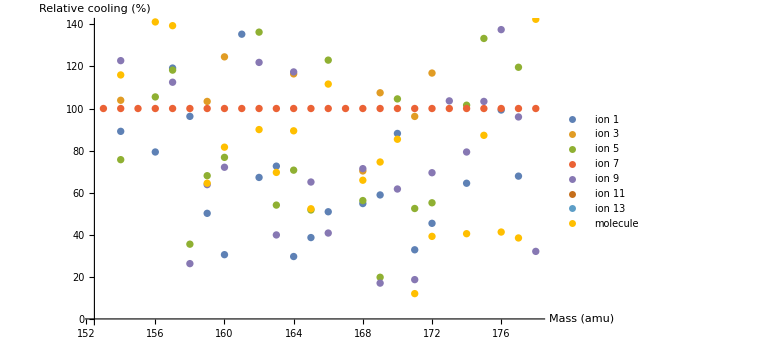
Sympathetic Cooling (all ions Doppler-cooled) as a percentage of ion 7 cooling rate @0.1K -Graphics-Top

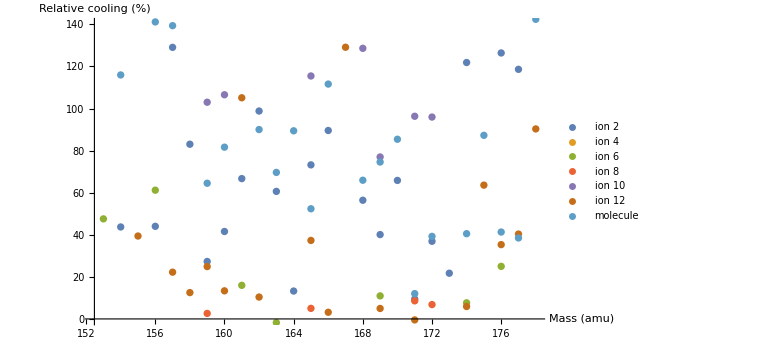
Sympathetic Cooling (all ions Doppler-cooled) as a percentage of ion 7 cooling rate @0.1K -Graphics-Top

```mathematica
res2=Transpose[AllSCDiffMNO[#,Num,Num]&/@(1.66*^-27*Range[startmass,endmass])];
Labeled[ListPlot[Append[res2[[#;;Num-1;;2]],res2[[Num]]],DataRange->{startmass,endmass},ImageSize->Large,PlotLegends->Append[Table["ion "<>ToString[i],{i,#,Num-1,2}],"molecule"],PlotRange->{0,140},Axes->True,AxesLabel->{"Mass (amu)","Relative cooling (%)"}]"Sympathetic Cooling (all ions Doppler-cooled) as a percentage of ion 7 cooling rate @"<>ToString[N[tempK]]<>"K",Top]&[1]
Labeled[ListPlot[Append[res2[[#;;Num-1;;2]],res2[[Num]]],DataRange->{startmass,endmass},ImageSize->Large,PlotLegends->Append[Table["ion "<>ToString[i],{i,#,Num-1,2}],"molecule"],PlotRange->{0,140},Axes->True,AxesLabel->{"Mass (amu)","Relative cooling (%)"}]"Sympathetic Cooling (all ions Doppler-cooled) as a percentage of ion 7 cooling rate @"<>ToString[N[tempK]]<>"K",Top]&[2]
```

## 3 Plasma Approach

## 3.1 Prep

```mathematica
(*variables*)
mt=mi+mj;T0=0.5*(mi*ui^2+mj*uj^2);V=(mi*ui+mj*uj)/mt;T0d=T0-0.5*mt*V^2;μ=mi*mj/mt//Simplify;tmax=0.01;
```

```mathematica
(*mathieu trajectories*)
D2n[n_]:=(a-(2*n+β)^2)/q;
recur[i_,stop_,dir_]:=1/(D2n[i*dir]-If[i≥stop,0,recur[i+1,stop,dir]])//FullSimplify;

getBetaEQ[ordD_,ordAQ_]:=Normal[Series[a-q*(recur[1,ordD+1,1]+recur[1,ordD+1,-1])/.{a->ϵ*a,q->ϵ*q,β->ϵ*β},{ϵ,0,ordAQ+1}]]/.{ϵ->1};
solveMathieu[ordD_,ordAQ_]:=Solve[β^2==getBetaEQ[ordD,ordAQ],β,PositiveReals]//FullSimplify (*This is just for ease of use*)

rMat[A0_,B0_,ad_,qd_,ord_]:=Module[{C2n=recur[#,ord,1]&/@Range[ord],Cn2n=recur[#,ord,-1]&/@Range[ord]},
C2n=Apply[Times,C2n[[;;#]]]&/@Range[ord];Cn2n=Apply[Times,Cn2n[[;;#]]]&/@Range[ord];
(A0*Cos[β*t]+B0*Sin[β*t])+Sum[C2n[[n]]*(A0*Cos[(2*n+β)*t]+B0*Sin[(2*n+β)*t])+Cn2n[[n]]*(A0*Cos[(-2*n+β)*t]+B0*Sin[(-2*n+β)*t]),{n,1,ord}]/.Normal[solveMathieu[ord,ord]]/.{a->ad,q->qd}//FullSimplify]
```

```mathematica
(*magic*)
Δp=-4*μ*b^2*(ri-rj)*Sqrt[2*μ*T0d]*(ui-uj)/(b^2+(rj-ri)^2)^2//FullSimplify;
dpdt=dplldt*ui//FullSimplify;
b0=Table[Abs[z0M[[1]]-z0M[[i]]]*l0/.solnsMOTION,{i,2,Num}];db=5*^-6;
```

## 3.2 Setup

```mathematica
ahold=0.01;qhold=0.1;ordhold=3;βhold=Normal[solveMathieu[4,4]][[1]];mi=171*1.66*^-27;mj=138*1.66*^-27;
iIC={0,31.189};jIC={0,3.471};
```

```mathematica
ri[td_]:=Evaluate[rMat[Ai,Bi,ahold*mi/mj,qhold*mi/mj,ordhold]/.{t->td*0.5*wmhz*w/.solnsMOTION}][[1]];rj[td_]:=Evaluate[rMat[Aj,Bj,ahold,qhold,ordhold]/.{t->td*0.5*wmhz*w/.solnsMOTION}][[1]];
ui[td_]:=D[ri[t],t]/.{t->td};uj[td_]:=D[rj[t],t]/.{t->td};
```

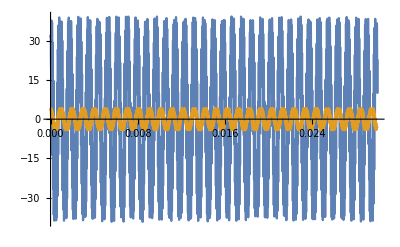

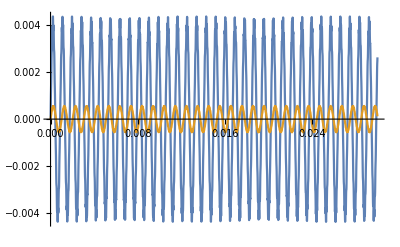

```mathematica
iVals=Solve[{ri[0]==iIC[[1]],ui[0]==iIC[[2]]},{Ai,Bi}][[1]];
jVals=Solve[{rj[0]==jIC[[1]],uj[0]==jIC[[2]]},{Aj,Bj}][[1]];
rif[t_]:=ri[t]/.iVals//FullSimplify;rjf[t_]:=rj[t]/.jVals//FullSimplify;
uif[t_]:=ui[t]/.iVals//FullSimplify;ujf[t_]:=uj[t]/.jVals//FullSimplify;

Plot[{Evaluate[Re[uif[t]]],Evaluate[Re[ujf[t-0.003]]]},{t,0,0.03}]
Plot[{Evaluate[Re[rif[t]]],Evaluate[Re[rjf[t]]]},{t,0,0.03}]
```

## 3.3 Average over Mathieu trajectories

```mathematica
ri1[td_]:=Evaluate[rMat[Ai1,Bi1,ahold*mi/mj,qhold*mi/mj,ordhold]/.{t->td*0.5*wmhz*w/.solnsMOTION}][[1]];
ri2[td_]:=Evaluate[rMat[Ai2,Bi2,ahold*mi/mj,qhold*mi/mj,ordhold]/.{t->td*0.5*wmhz*w/.solnsMOTION}][[1]];
ui1[td_]:=D[ri1[t],t]/.{t->td};ui2[td_]:=D[ri2[t],t]/.{t->td};
iVals2=Solve[{ri1[0]==iIC[[1]],ui1[0]==iIC[[2]]},{Ai1,Bi1}][[1]];Ai1=Ai1/.iVals2;Bi1=Bi1/.iVals2;
```

```mathematica
fn[td_]:=Sum[(Cos[(2*n+β)*td]-Cos[(2*n+β)*(td-2*t0)])/(2*n+β),{n,-ordhold,ordhold}]/.βhold/.{a->ahold,q->qhold}
```

```mathematica
newAidBid=Solve[{ri1[t0]==ri2[t0],ui2[t0]-ui1[t0]==dphold},{Ai2,Bi2}][[1]]/.{dphold->Δp};
Ai2=Chop[Ai2/.newAidBid]//Simplify;Bi2=Chop[Bi2/.newAidBid]//Simplify;
```

```mathematica
ri2h=Evaluate[rMat[Ai2h,Bi2h,ahold*mi/mj,qhold*mi/mj,ordhold]/.{t->t*0.5*wmhz*w/.solnsMOTION}][[1]];
ui2h=D[ri2h,t];
ri2h=Chop[ri2h/.{Ai2h->Ai2,Bi2h->Bi2}]//Simplify;
ui2h=Chop[ui2h/.{Ai2h->Ai2,Bi2h->Bi2}]//Simplify;
```

```mathematica
ΔEi=0.5*mi*(ui2h^2-ui1[t0]^2);
```

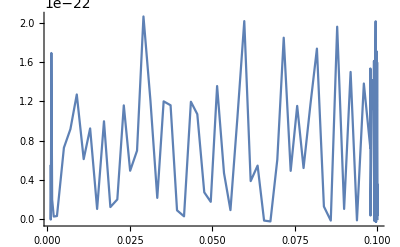

```mathematica
Plot[Evaluate[ΔEi/.{t0->0.002}],{t,0.001,0.1}]
```

## 3.4 Spitzer Approach

```mathematica
ParallelSum[NIntegrate[ΔEi,{b,b0[[i]]-db,b0[[i]]+db},{t0,0,0.01},{t,0,0.01}],{i,Num-1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.30474×10^-36 and 2.3616×10^-33 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.30474×10^-36 and 2.3616×10^-33 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.30474×10^-36 and 2.3616×10^-33 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.30474×10^-36 and 2.3616×10^-33 for the integral and error estimates.

4.29616×10^-35

```mathematica
mt=mi+mj;k=8.9875*^9;e=1.602*^-19;mj=138*1.66*^-27;kb=1.38*^-23;eps=0.533;rho=(Num-1)/(Pi*b0[[-1]]*(5*^-4)^2);
b0=Table[Abs[z0M[[1]]-z0M[[i]]]*l0/.solnsMOTION,{i,2,Num}];
```

```mathematica
Ej=kb*0.1*0.5;Ei=4*e;
```

```mathematica
dEidt=Sum[-2*k*e^3*mi*mj/mt^2/Sqrt[2*mi*Ei^3]*(1-mj/mi*eps)*(Ei-Ej)*Log[1+(Ei*b0[[n]]/(k*e^2))^2],{n,Num-1}]//FullSimplify
```

(6.28437×10^-85-5.14692×10^-60 mi)/(√mi (2.2908×10^-25+mi)^2)

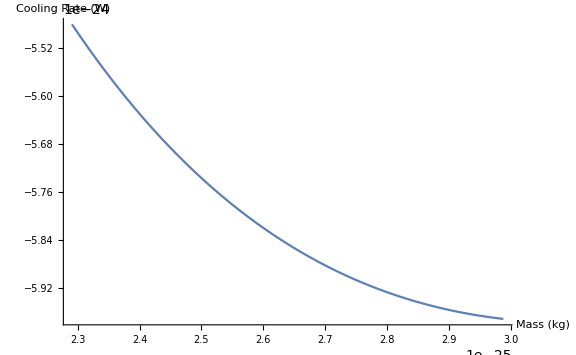

```mathematica
Plot[Evaluate[dEidt],{mi,138*1.66*^-27,180*1.66*^-27},ImageSize->Large,Axes->True,AxesLabel->{"Mass (kg)","Cooling Rate (W)"}]
```

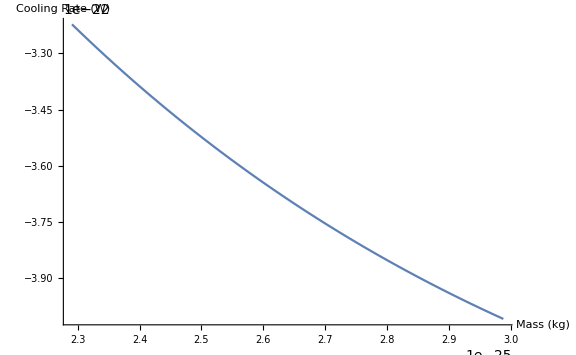

```mathematica
Plot[Evaluate[-2mi*mj/(mi+mj)^2*(1-mj/mi*0.533)*(Ki-Kj)],{mi,138*1.66*^-27,180*1.66*^-27},ImageSize->Large,Axes->True,AxesLabel->{"Mass (kg)","Cooling Rate (W)"}]
```

## 3.5 Force in z-direction

```mathematica
Δpperp=-4*μ*b*(ri-rj)/(b^2+(ri-rj)^2)*(ui-uj);
Δpperp=Integrate[Δpperp,b];d2=Δpperp/.{b->b2};d1=Δpperp/.{b->b1};
Δpperp=d2-d1//FullSimplify;
```

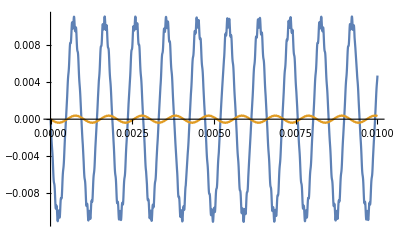

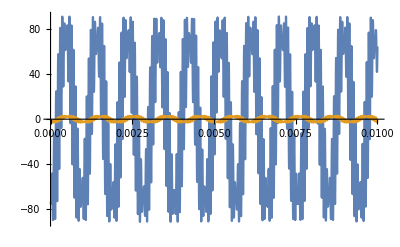

```mathematica
iVals3=Solve[{ri[0]==iIC[[1]],0.5*mi*ui[0]^2==0.5*kb*100},{Ai,Bi}][[1]];
jVals3=Solve[{rj[0]==jIC[[1]],0.5*mj*uj[0]^2==0.5*kb*0.1},{Aj,Bj}][[1]];
Δpperp=Δpperp/.{ri->ri[ti],rj->rj[tj],ui->ui[ti],uj->uj[tj]}/.iVals3/.jVals3//Simplify;

Plot[{Evaluate[ri[t]/.iVals3],Evaluate[rj[t]/.jVals3]},{t,0,tmax}]
Plot[{Evaluate[ui[t]/.iVals3],Evaluate[uj[t]/.jVals3]},{t,0,tmax}]
```

```mathematica
f[n_]:=NIntegrate[(Δpperp)^2/.{b2->b0[[1]]+db,b1->b0[[1]]-db},{ti,0,n*tmax},{tj,0,n*tmax}]/(n*tmax)^2
```

```mathematica
th=ParallelTable[f[i],{i,1,30}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.58258×10^-61 and 1.37027×10^-61 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.59198×10^-60 and 4.79269×10^-61 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.02171×10^-61 and 8.40783×10^-62 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.52558×10^-62 and 2.69226×10^-63 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.26637×10^-60 and 4.84755×10^-61 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.75855×10^-61 and 1.1509×10^-61 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.22968×10^-60 and 2.75735×10^-61 for the integral and error estimates.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.66862×10^-62 and 1.79666×10^-62 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.28429×10^-60 and 6.46707×10^-61 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.56718×10^-61 and 1.70438×10^-61 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.39045×10^-60 and 3.75191×10^-61 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.92636×10^-61 and 4.12572×10^-62 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.70638×10^-60 and 7.61323×10^-61 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ti near {ti,tj} = {0.0307183,0.177266}. NIntegrate obtained 3.84965×10^-60 and 8.21036×10^-61 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ti near {ti,tj} = {0.0226811,0.211031}. NIntegrate obtained 4.04099×10^-60 and 6.96145×10^-61 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.08542×10^-60 and 1.79316×10^-60 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.88641×10^-60 and 1.49084×10^-60 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.5877×10^-60 and 4.79403×10^-61 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ti near {ti,tj} = {0.146043,0.244796}. NIntegrate obtained 2.68143×10^-60 and 7.90982×10^-61 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.63651×10^-60 and 1.06016×10^-60 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ti near {ti,tj} = {0.140843,0.248957}. NIntegrate obtained 6.40109×10^-60 and 1.49717×10^-60 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.44946×10^-60 and 8.61454×10^-61 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ti near {ti,tj} = {0.0675829,0.253237}. NIntegrate obtained 4.82577×10^-60 and 1.31423×10^-60 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.77666×10^-60 and 1.03412×10^-60 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.05902×10^-60 and 1.26012×10^-60 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

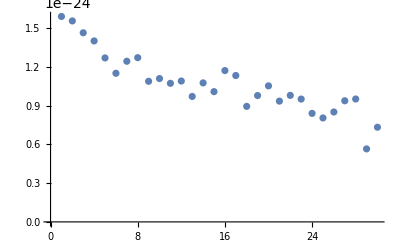

```mathematica
ListPlot[Sqrt[th]/(2*db)]
```

```mathematica
154*1.66*^-27*(0.07*wmhz)^2*Abs[z0M[[1]]*l0]-ke2*Sum[L0Mn[1,i,-2],{i,2,Num}]/l0^2/.{U->10}
```

1.28911×10^-18

```mathematica
dEidt=Sum[k*e^3/Sqrt[2*mi*Ei^3]*Log[1+(Ei*b0[[n]]/(k*e^2))^2],{n,Num-1}]//FullSimplify
```

0.0000329045

```mathematica
Max[Sqrt[th]/(2*db)]/dEidt
```

4.81451×10^-20

```mathematica
(*force to beat*)
kz/.solnsMOTION
```

9.23875×10^-16

```mathematica
tempj=1*^-3;tempi=100;kappa=ke2/2/(kb*(tempi+tempj));
mwr2=κr^2*3.25*^-40*V0^2/w^2/r0^4/m0+1.602*^-13*(κr*V1/r0^2-κz*U/z0^2)/.{solnsMOTION}[[1]];
```

```mathematica
dr=Sqrt[kb*tempj/mwr2];dz=b0[[Num-1]];ρ=(Num-1)/(Pi*dr^2*dz);
Ki=kb*tempi;Kj=kb*tempj;vj=Sqrt[2*kb*tempj/m0];K0d=((Ki+Kj)-0.5*((Sqrt[2*mi*Ki]+vj*mj))^2/(mi+mj));
```

```mathematica
FCC[mi_]:=Module[{vi=Sqrt[2*kb*tempi/mi],kappa},
kappa=ke2/2/(Ki+Kj-0.5*(mi*vi-m0*vj)^2);
ρ*ke2*(Total[b0]-kappa*(Total[ArcTan[#/kappa]&/@b0]))*Ki/(Ki+Kj-0.5*(mi*vi-m0*vj)^2)*mi/(mi+m0)]
```

```mathematica
FCC[171*1.66*^-27]
```

1.71179×10^-14

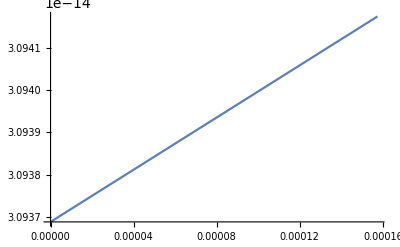

```mathematica
Plot[FCC[mi],{mi,138*1.66^-27,200*1.66*^-27}]
```

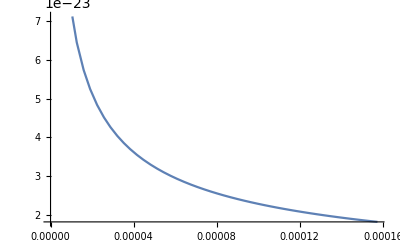

```mathematica
Plot[Evaluate[mi*mj/(mi+mj)/Sqrt[mi]],{mi,138*1.66^-27,200*1.66*^-27}]
```

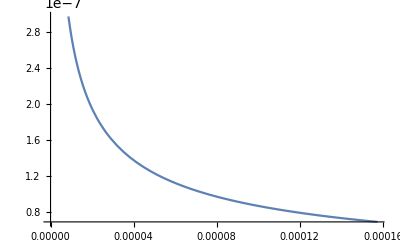

```mathematica
Plot[Evaluate[mj*Sqrt[2*mi*Ki]/(mi+mj)/K0d],{mi,138*1.66^-27,200*1.66*^-27}]
```